```mathematica
SetDirectory[NotebookDirectory[]];
w1=Import["1.dat"];
w2=Import["2.dat"];
w3=Import["RK_2.dat"];
w4=Import["S.dat"];
```

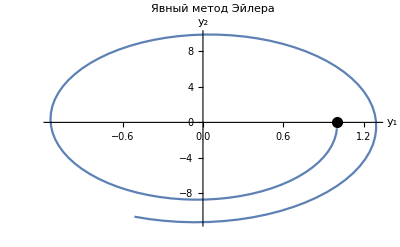

```mathematica
Show[ListLinePlot[w1, AxesLabel->{Subscript[y, 1],Subscript[y, 2]}, PlotLabel->"Явный метод Эйлера"],Graphics[{PointSize[0.02],Point[{1,0}]}]]
```

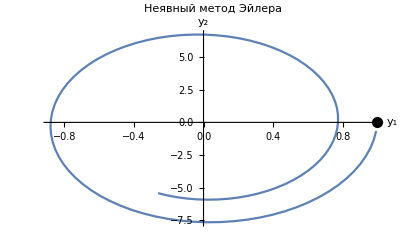

```mathematica
Show[ListLinePlot[w2,AxesLabel->{Subscript[y, 1],Subscript[y, 2]},PlotLabel->"Неявный метод Эйлера"],Graphics[{PointSize[0.02],Point[{1,0}]}]]
```

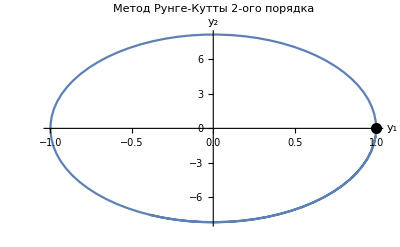

```mathematica
Show[ListLinePlot[w3,AxesLabel->{Subscript[y, 1],Subscript[y, 2]},PlotLabel->"Метод Рунге-Кутты 2-ого порядка"],Graphics[{PointSize[0.02],Point[{1,0}]}]]
```

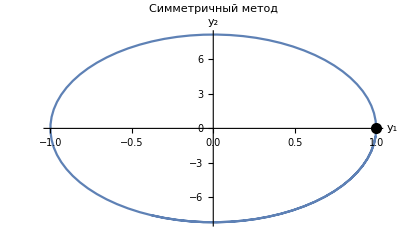

```mathematica
Show[ListLinePlot[w4,AxesLabel->{Subscript[y, 1],Subscript[y, 2]}, PlotLabel->"Симметричный метод"],Graphics[{PointSize[0.02],Point[{1,0}]}]]
```